```mathematica
MF2[λ_,η_,γ_]:=Block[{cp=.12,cπ=.08},
NDSolveValue[{
prey'[t]==λ-Min[cπ/cp,1]pred[t]prey[t]-(η+cp)prey[t],
pred'[t]==γ Min[cπ/cp,1]pred[t]prey[t]-(η+cπ)pred[t],
pred[0]==1,prey[0]==1
},{prey,pred},{t,0,100}]
]
```

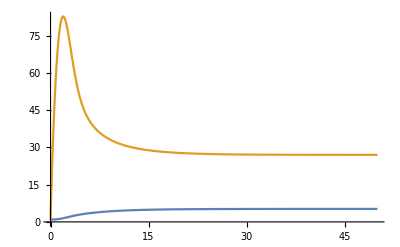

```mathematica
mf=MF[100,0.1,.01];
Plot[{mf[[1]][t],mf[[2]][t]},{t,0,50}]
```

```mathematica
T=100
```

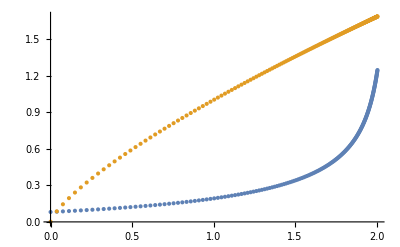

```mathematica
ListPlot[
{ParallelTable[
mf=MF[λ,0.05,.1];
{mf[[2]][T],mf[[1]][T]},{λ,0,2,.01}],
ParallelTable[
mf=MF[λ,0.05,.1];
{mf[[2]][T],mf[[2]][T]^(3/4)},{λ,0,2,.01}]
},PlotRange->All
]
```

```mathematica
MF3[λ_,η_,γ_]:=Block[{cp=.12,cπ1=.08,cπ2=.08},
NDSolveValue[{
prey'[t]==λ-Min[cπ1/cp,1]pred1[t]prey[t]-(η+cp)prey[t],
pred1'[t]==γ Min[cπ1/cp,1]pred1[t]prey[t]-Min[cπ2/cπ1,1]pred1[t]pred2[t]-(η+cπ1)pred1[t],
pred2'[t]==γ Min[cπ2/cπ1,1]pred1[t]pred2[t]-(η+cπ2)pred2[t],
pred1[0]==1,pred2[0]==1,prey[0]==1
},{prey,pred1,pred2},{t,0,1000}]
]
```

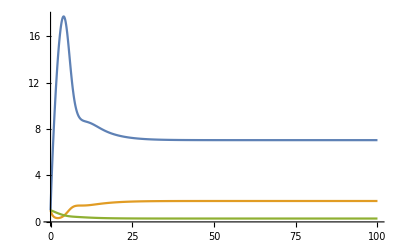

```mathematica
mf=MF3[10,0.1,.1];
Plot[{mf[[1]][t],mf[[2]][t],mf[[3]][t]},{t,0,100}]
```

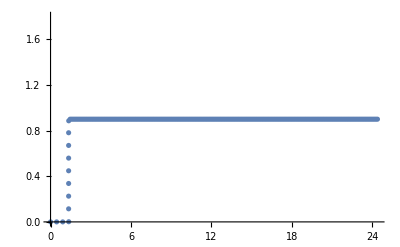

```mathematica
T=500;
ListPlot[
ParallelTable[
mf=MF3[λ,0.1,.2];
{mf[[1]][T],mf[[2]][T]},{λ,0,20,.1}]
]
```

prey = {{i, κ, cp}}

```mathematica
neighbour[graph_][site_]:=RandomChoice[AdjacencyList[graph,site]]
```

```mathematica
move[graph_][preyPop_]:=MapAt[neighbour[graph],#,Key["site"]]&/@preyPop
graze[graph_][preyPop_,grass_]:=MapAt[neighbour[graph],#,Key["site"]]&/@preyPop
```

```mathematica
Do[

]
```